#### Sezione e.

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[μ_,x_]:= μ x (1-x)
fn[μ_,x_,n_]:= Nest[f[μ,#]&,x,n]
```

```mathematica
(*Manipulate[ListPlot[fn[μ,0.4,#]&/@Range[100]],{μ,0,4}]*)
```

```mathematica
fnC=Compile[{{μ,_Real},{x,_Real},{n,_Integer}},Nest[μ #(1-#)&,x,n]]
```

CompiledFunction[…]

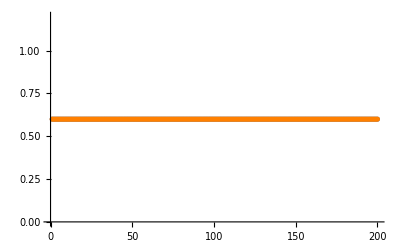

```mathematica
Show[ListPlot[fn[2.5,0.4,#]&/@Range[200]],ListPlot[fn[2.5,0.4001,#]&/@Range[200],PlotStyle->Orange]]
```

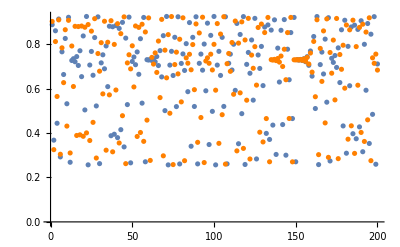

```mathematica
Show[ListPlot[fn[3.7,0.4,#]&/@Range[200]],ListPlot[fn[3.7,0.4+10^14 $MachineEpsilon,#]&/@Range[200],PlotStyle->Orange]]
```

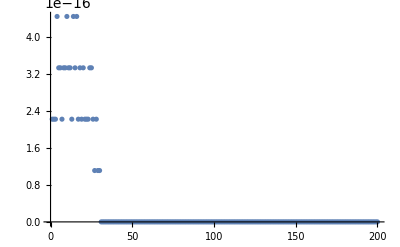
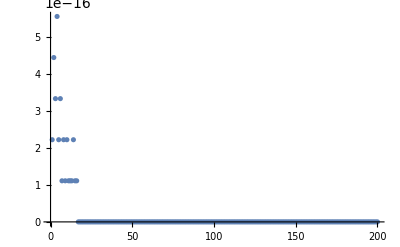
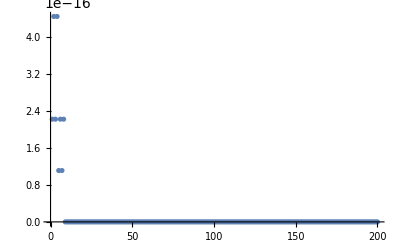
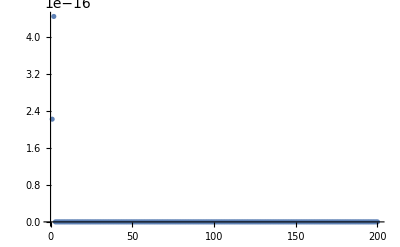
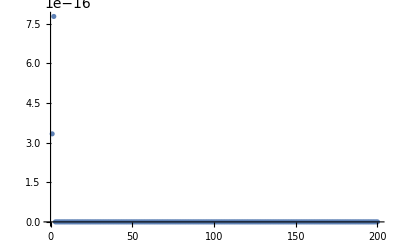
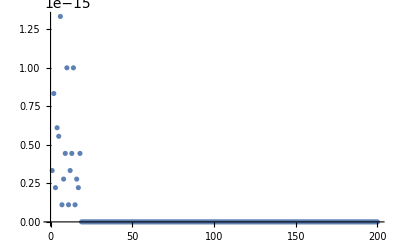
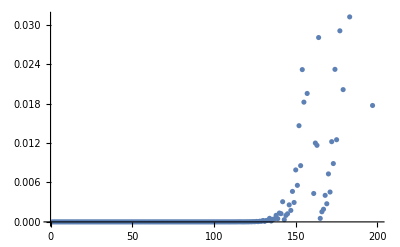
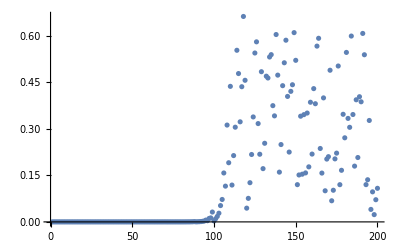

```mathematica
Table[ListPlot[Abs[fn[μ,0.4,#]-fn[μ,0.4+2 $MachineEpsilon,#]]&/@Range[200]],{μ,3,4,0.1}]
```

mmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmm

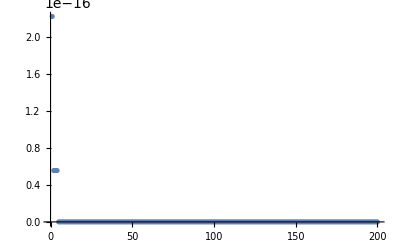

```mathematica
ListPlot[Abs[fn[2,0.4,#]-fn[2,0.4+2 $MachineEpsilon,#]]&/@Range[200]]
```

si vede che fino a μ>μ_∞ le orbite si “appiccicano per bene”, poi la separazione avviene

facciamo un po’ di giochini

```mathematica
modfprime[μ_,x_]:=Abs[D[f[μ,x],x]]
```

```mathematica
D[f[μ,x],x]
```

(1-x) μ-x μ

```mathematica
values1=fn[3,0.4,#]&/@Range[200];
```

```mathematica
values2=fn[3.5,0.4,#]&/@Range[200];
```

```mathematica
values3=fn[3.8,0.4,#]&/@Range[200];
```

```mathematica
check[μ_]:= ListPlot[Abs[(1-#) μ-# μ]&/@fn[μ,0.4,#]&/@Range[200]]
```

```mathematica
Manipulate[check[μ],{μ,3,4}]
```

non ho ben capito che farci con gli esponenti di lyapunov ma ok

allora fondamentalmente (topo che fotte la anime femmina)
|δz(t)|≤Cⅇ^λt|δz(0)|, se λ>0 allora la dinamica è caotica ove z=f_μ
come determino λ?
(| δf_μ(t) |)/(|δf_μ(0)|)≤Cⅇ^λt in realtà possiamo incorporare |δf_μ(0)| nella costante C e studiare il modulo della derivata

```mathematica
D[f[μ,x], x]
```

(1-x) μ-x μ

```mathematica
dfn[μ_,x_,n_]:=RealAbs[D[fn[μ,ξ,n], ξ]]/.{ξ->x}
```

```mathematica
plotλ[μ_,x0_]:=ListPlot[1/# Log[dfn[μ,x0,#]]&/@Range[1,14]]
```

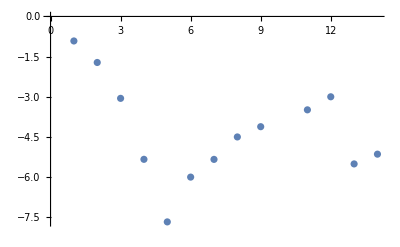
{3.125,-Graphics-}

```mathematica
plotλ[2,0.4]//Timing
```

funziona? circa
è veloce? AHAHAHAHAHA
se provassi a farlo con incrementi finiti?
tipo rimpiazzo la derivata col rapporto incrementale

```mathematica
fakedfn[μ_,x_,n_]:=1/(2$MachineEpsilon)RealAbs[fn[μ,x,n]-fn[μ,x+2$MachineEpsilon,n]]
```

```mathematica
plotλ2[μ_,x0_]:=ListPlot[1/# Log[fakedfn[μ,x0,#]]&/@Range[1000]]
```

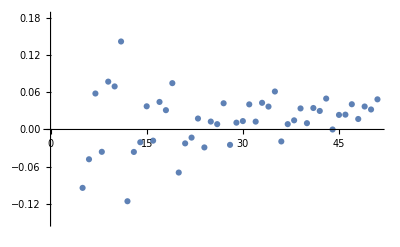

```mathematica
plotλ2[3.57,0.774]
```

meno preciso ma cazzo quant’è più veloce
come “limite” rimane abbastanza caotico ma prendiamo un valore di n abbastanza grosso e cioa, 2000 è arbitrario ma dovrebbe bastare per far sì che i conti non siano troppo lenti.

```mathematica
fakelimit[μ_,x0_]:=1/2000 Log[fakedfn[μ,x0,2000]]
```

```mathematica
Manipulate[fakelimit[3.57,x],{x,0,1}] (*non tutti i valori di x sono validi per questo*)
```

se il limite non esiste (f.ind) è perché i valori convergono a 0 prima dello step 2000(che sto usando per il limite) e log(0) ∄ ofc

```mathematica
First@Cases[{#,fakelimit[#,0.6]}&/@Range[3.569,3.57,10^-6],{_,_Real}]
```

{3.56967,0.00113863}

(che è il nostro μ_∞, tasbora fioi)